```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
{NN,RR} = Dimensions[S];
λplusof[ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];λminusof[ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
J =Table[λplusof[ρ]- λminusof[ρ],{ρ,1,RR}];
J //MatrixForm
```

(-x[1] k_-[1]+k_+[1]
-x[1] k_-[2]+x[2] k_+[2]
-x[1]^3 k_-[3]+x[1]^2 x[2] k_+[3])

```mathematica
S.J //MatrixForm
```

(-x[1] k_-[1]-x[1] k_-[2]-x[1]^3 k_-[3]+k_+[1]+x[2] k_+[2]+x[1]^2 x[2] k_+[3]
x[1] k_-[2]+x[1]^3 k_-[3]-x[2] k_+[2]-x[1]^2 x[2] k_+[3])

```mathematica
ss = Simplify@Solve[S.J == 0, Table[x[i],{i,1,NN}]][[1]]
```

{x[1]→(k_+[1])/(k_-[1]),x[2]→((k_-[1])^2 k_-[2] k_+[1]+k_-[3] (k_+[1])^3)/((k_-[1])^3 k_+[2]+k_-[1] (k_+[1])^2 k_+[3])}

```mathematica
Subscript[J, ss]= FullSimplify[J /.ss]
```

{0,((k_+[1])^3 (k_-[3] k_+[2]-k_-[2] k_+[3]))/((k_-[1])^3 k_+[2]+k_-[1] (k_+[1])^2 k_+[3]),((k_+[1])^3 (-k_-[3] k_+[2]+k_-[2] k_+[3]))/((k_-[1])^3 k_+[2]+k_-[1] (k_+[1])^2 k_+[3])}

```mathematica
F[x1_,x2_] = S.J/.{x[1]->x1,x[2]->x2}
```

{-x1 k_-[1]-x1 k_-[2]-x1^3 k_-[3]+k_+[1]+x2 k_+[2]+x1^2 x2 k_+[3],x1 k_-[2]+x1^3 k_-[3]-x2 k_+[2]-x1^2 x2 k_+[3]}

```mathematica
stab = FullSimplify[Grad[S.J,{x[1],x[2]}]/.ss]
```

{{-k_-[1]+k_-[2]-(k_-[3] (k_+[1])^2)/(k_-[1])^2-(2 ((k_-[1])^2 k_-[2]+k_-[3] (k_+[1])^2) k_+[2])/((k_-[1])^2 k_+[2]+(k_+[1])^2 k_+[3]),k_+[2]+((k_+[1])^2 k_+[3])/(k_-[1])^2},{k_-[2]+(3 k_-[3] (k_+[1])^2)/(k_-[1])^2-(2 (k_+[1])^2 ((k_-[1])^2 k_-[2]+k_-[3] (k_+[1])^2) k_+[3])/((k_-[1])^4 k_+[2]+(k_-[1])^2 (k_+[1])^2 k_+[3]),-k_+[2]-((k_+[1])^2 k_+[3])/(k_-[1])^2}}

```mathematica
simp = { SubPlus[k][1] -> 1,SubMinus[k][1]->1,SubPlus[k] [2] ->1, SubMinus[k][2]->α,SubPlus[k][3]->β,  SubMinus[k][3]->1}
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→α,k_+[3]→β,k_-[3]→1}

```mathematica
T =FullSimplify[ Tr[stab]]/.simp //Together
```

(-5-α-4 β+α β-β^2)/(1+β)

```mathematica
DD = FullSimplify[Det[stab]]/.simp
```

1+β

```mathematica
Subscript[α, c] := (5 + 4β + β^2)/(β-1) (* β needs to be greater than 1 if we want α to be positive *)
```

```mathematica
T /. α ->  Subscript[α, c]//FullSimplify
```

0

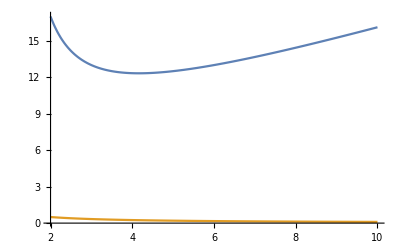

```mathematica
Plot[{(5 + 4β + β^2)/(β-1), 1/β},{β, 2, 10},PlotRange->All]
```

```mathematica
Subscript[F, t] = S.J /. Table[x[i]->x[i][t],{i,1,NN}]/.simp
Subscript[α, c]/.β -> 3(* α needs to be greater than Subscript[α, c](β), fixed β, in order to have limit cycles *)
```

{1-x[1][t]-α x[1][t]-(x[1][t])^3+x[2][t]+β (x[1][t])^2 x[2][t],α x[1][t]+(x[1][t])^3-x[2][t]-β (x[1][t])^2 x[2][t]}

13

```mathematica
EQS=Table[D[x[i][t],t]==Subscript[F, t][[i]],{i,1,NN}]/.{α -> 13.001,β ->3};EQS//MatrixForm
IC={x[1][0]==ss[[1]]+1,x[2][0]==ss[[2]]+1};
vars = Table[x[i][t],{i,1,NN}];
```

(x[1]'[t]==1-14.001 x[1][t]-(x[1][t])^3+x[2][t]+3 (x[1][t])^2 x[2][t]
x[2]'[t]==13.001 x[1][t]+(x[1][t])^3-x[2][t]-3 (x[1][t])^2 x[2][t])

{x[1][t]→InterpolatingFunction[…][t],x[2][t]→InterpolatingFunction[…][t]}

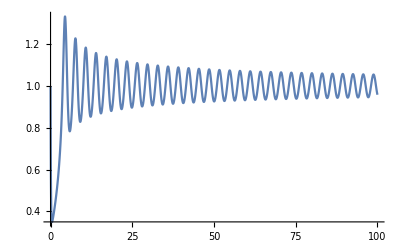

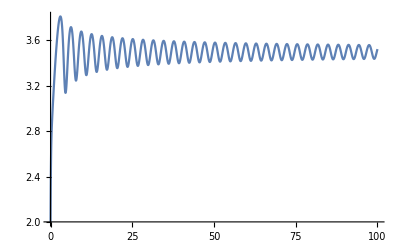

```mathematica
Subscript[t, max]=100;
sols=NDSolve[{EQS,x[1][0] == 1, x[2][0] ==2},vars,{t,0,Subscript[t, max]}][[1]]
Plot[x[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[x[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

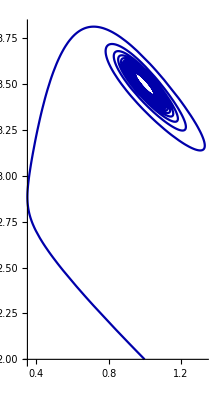

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->200,PlotStyle->Darker@Blue]
```

```mathematica
J /.ss /. simp /. α ->1/β//MatrixForm //FullSimplify (* The reversibility is given by α = 1/β *)
```

(0
0
0)

```mathematica
J /. simp //FullSimplify //MatrixForm
```

(1-x[1]
-α x[1]+x[2]
x[1]^2 (-x[1]+β x[2]))

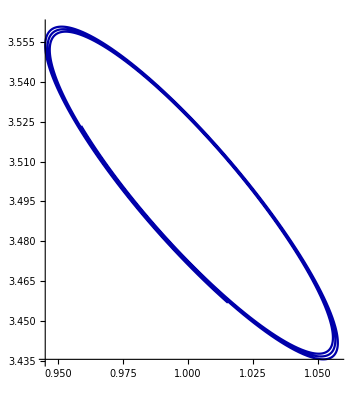

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.sols,{t,Subscript[t, max]*0.9,Subscript[t, max]},PlotRange->All,PlotPoints->500,PlotStyle->Darker@Blue]
```